# Examples using the Teukolsky package

This package is still in heavy development. This notebook demonstrates some of the currently implemented features.

```mathematica
<<Teukolsky`
```

## Homogeneous solutions

```mathematica
R=TeukolskyRadial[-2,2,2,0.9,0.1]
```

TeukolskyRadialFunction[-2,2,2,0.9,0.1,<<>>]

```mathematica
R[10.]
R["In"][10.]
```

<|In→6463.62+2139.25 ⅈ,Up→642.476-546.172 ⅈ|>

6463.62+2139.25 ⅈ

```mathematica
R'[10.]
```

<|In→2599.24+1501.96 ⅈ,Up→-311.575+18.0816 ⅈ|>

```mathematica
R''[10.]
```

<|In→669.088+746.961 ⅈ,Up→-19.9639+21.0428 ⅈ|>

Using the field equation the package will allow you to take as many derivatives as you want

```mathematica
R'''''[10.]
```

<|In→-11.3332-4.68713 ⅈ,Up→-1.32356-2.18908 ⅈ|>

The homogeneous solutions are asymptotically unit normalized. e.g., lim_(r→∞) |R^up(r)/r^3|=1

```mathematica
Rdata=Table[{r,R["Up"][r]/r^3//ReIm}//Flatten,{r,10.,300.,1.}];
```

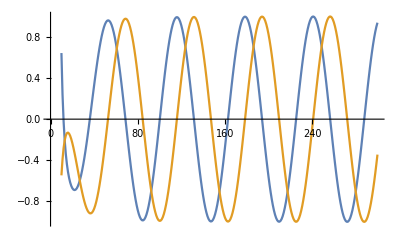

```mathematica
ListPlot[{Rdata[[;;,{1,2}]],Rdata[[;;,{1,3}]]},Joined->True]
```

## Renormalized angular momentum

There are two methods for computing the renormalized angular momentum. The series method is not yet fully implemented (but is the default). The Monodromy method is usually robust so long as high precision values are entered. Note also that the input parameter is ϵ = 2Mω. This will likely change soon to be ω.

```mathematica
RenormalizedAngularMomentum[1,2,1,0.9`32,0.5`32,Method->"Monodromy"]
```

1.899810315856009681920152

## Fluxes (s=-2) circular, equatorial only

Currently the Teukolsky source has only been implemented for s=-2 and for circular, equatorial orbits

```mathematica
a=0.9`32;
r0=10.`32;
```

```mathematica
orbit=KerrGeoOrbit[a,r0,0,1]
```

KerrGeoOrbitFunction[0.90000000000000000000000000000000,10.000000000000000000000000000000,0,1.,<<>>]

```mathematica
s=-2;l=2;m=2;n=0;k=0;
mode=TeukolskyPointParticleMode[s,l,m,n,k,orbit]
```

TeukolskyModeObject[-2,2,2,0,0,<<>>]

```mathematica
2mode["Fluxes"]
```

<|FluxInf→0.00004454600110236099,FluxHor→-1.1967358426766726×10^-7,FluxTotal→0.00004442632751809333|>

```mathematica
R=mode["Radial"]
```

TeukolskyRadialFunction[-2,2,2,0.90000000000000000000000000000000,0.06149536444857092909254283058,<<>>]

```mathematica
R[r0]
```

<|In→6923.43762519192312+349.53753071987891 ⅈ,Up→8719.11896417092391-2411.28850085561695 ⅈ|>